```mathematica
μ = 5;
αtotal = 10;
r = αtotal/μ;
κ = 0.05;
```

```mathematica
shift=Table[RandomVariate[GammaDistribution[(1-κ)*αtotal, 1/r]],{i,1,100}];
```

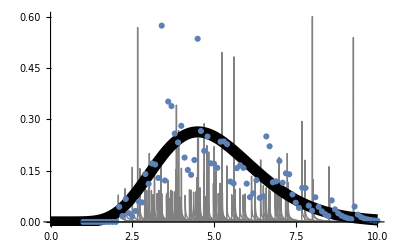

```mathematica
xvals=Range[1,10,0.1];
scaleval=200;
Show[
Plot[1/scaleval*PDF[GammaDistribution[κ*αtotal, 1/r],x-shift],{x,0,10}, PlotStyle->{Gray,Thin}, PlotRange->All],
Plot[PDF[GammaDistribution[αtotal, 1/r],x],{x,0,10}, PlotStyle->{Black,Thickness[0.02]}],
ListPlot[{
xvals,
Total[Table[PDF[GammaDistribution[κ*αtotal, 1/r], x-shift],{x,xvals}]ᵀ]/Length[shift]}ᵀ
]]
```